# Sequence Alignment Algorithms

## Introduction

Sequence alignment is the identification of residue-residue correspondences. It is the basic tool of bioinformatics.

Any assignment of correpondences that preserves the order of the residues within the sequences is an alignment. Gaps may be introduced.

Can you give at least two different alignments for strings “ABCDE” and “ACDEF”?

To find the best alignment we need to check all possibilities.

```mathematica
SequenceAlignment["gctgctataatc","ctataatc"]
```

{{gctg,},ctataatc}

Pairwise sequence alignment

Multiple sequence alignment

## The dotplot

Rows: Residues of one sequence

Columns: Residues of second sequence

Positions in the dotplot are filled if they match and blank when they are different

Stretches of similar residues show up as diagonals in the upper left-lower right

Can you write down the alignment of the sequences “DOROTHYHODGKIN” (rows) and “DOROTHYCROWFOOTHODGKIN” (columns) from below dotplot?

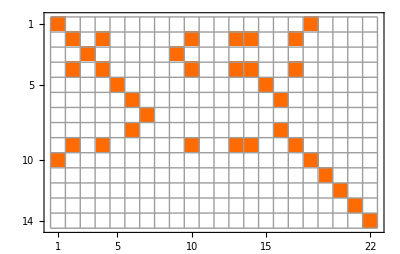

```mathematica
MatrixPlot[Outer[Boole[SameQ[#1,#2]]&,Characters["DOROTHYHODGKIN"],Characters["DOROTHYCROWFOOTHODGKIN"]], PlotLegends->{"Mismatch","Match"}, Mesh->True]
```

## Scoring Schemes

Scores as measures of sequence similarity

Similar sequences give high scores and dissimilar sequences give low scores

Optimization algorithms try to maximize the scoring function

Nucleic acid sequences

SIMPLE SCHEME: +1 for match and -1 for a mismatch

COMPLEX SCHEME: Accounts for higher frequency of transition mutations (purine ↔purine, pyrimidine↔pyrimidine) than transversion mutations (purine↔pyrimidine)

```mathematica
({{□, A, G, T, C}, {A, 20, 10, 5, 5}, {G, 10, 20, 5, 5}, {T, 5, 5, 20, 10}, {C, 5, 5, 10, 20}})
```

Protein sequences

Based on physicochemical type

Let the proteins guide us build the scoring matrix

Percent Accepted Mutation Matrix: First attempt by M.O Dayhoff who collected statistics on substitution frequencies in protein sequences then known

Blocks Substitution Matrices: Modification by Jorja Henikoff and Steven Henikoff

## PAM (Point Accepted Mutation Matrix)

Developed by Margaret Dayhoff (1978)

Derived from global alignments of sequences that are at least 85% identical

Is based on the observed rate of mutation during the predicted evolutionary changes in a smaller number of protein families.

Uses a rough measure of how many generations of evolution it would take to mutate one sequences into another

PAM matrices are identified by numbers and the general notation is PAM(N). The number ‘N’ provides a measure of evolutionary distance between the proteins being compared. A bigger number indicates greater evolutionary (mutational) distance. For example, the PAM1 matrix is calculated from comparisons of sequences that have diverged only 1 percent from each other.

Matrices such as PAM40, PAM100, PAM250 etc indicate greater evolutionary distances and are derived by extrapolation from those for lesser ones.

PAM matrices are most sensitive for alignments of sequences with evolutionary related homologs.

## BLOSUM (BLOck SUbstitution Matrix)

Developed by Jorjya Henikoff and Steven Henikoff (1992)

They are derived from local, ungapped alignments of distantly related sequences

All BLOSUM matrices are based on observed alignments; they are not extrapolated from comparisons of closely related proteins.

They are based on the concept of ‘blocks’-amino acid patterns derived from ungapped multiple alignments corresponding to the most conserved regions of a protein. These highly conserved sequences serve as protein signatures uniquely identifying them as distinct protein family.

They are derived from the observed amino acid substitutions in a large set of approximately 2000 such conserved patterns representing over 500 groups of related proteins.

As the with PAM matrices, BLOSUM matrices are also identified by numbers. The number after the matrix (e.g. BLOSUM62) refes to the minimum per cent identity of the blocks used to construct the matrix; greater the numbers mean lesser the distances.

BLOSUM62 is a matrix calculated from comparisons of sequences with no less than 62 per cent divergence.

## Relation between PAM and BLOSUM

Evolutionary distance: BLOSUM matrices are derived from alignments of distantly related sequences, the PAM matrices are derived from alignments of sequences that are closely related.

LOCAL vs. GLOBAL: BLOSUM matrices perform better than PAM matrices for local similarity searches. Compared to PAM60 matrix, the BLOSUM62 matrix was found to detect more distant relationships in a BLAST search

Short Queries: BLOSUM matrices does not perform well for short queries, so the older PAM matrices may be used for such searches.

## Computing the alignment of two sequences

Alignment techniques based on dynamic programming.

Optimal global alignment given choice of parameters - substitution matrix and gap penalty

Many alignments may give optimal score and none of these maybe biologically meaningful.

Not very good large database search due to computational difficulties (BLAST uses an approximation method).

Global alignment algorithm first applied to biological sequences by S.B Needleman and C.D Wunsch.

T. Smith and M. Waterman modified it to identify local matches.

There are three possible variations of alignment

Entire sequence 1 against entire sequence 2

Region of sequence 1 against entire sequence 2

Region of sequence 1 against region of sequence 2

### Dynamic Programming

#### Principle of Optimality

#### Memoization

### Optimal alignment problem

Given two character strings, possibly of unequal length - A=a_1 a_2... a_n and B=b_1 b_2... b_m - where each a_i and b_i is a member of an alphabet set 𝒜, consider sequences of edit operations that convert A and B to a common sequence. Individual edit opreations include:

Substitution of b_j for a_i is represented by (a_i,b_j)

Deletion of a_i from sequence A is represented by (a_i,ϕ)

Deletion of b_j from sequence B is represented by (ϕ,b_j)

Cost function 𝒹 is defined on edit operations:
𝒹(a_i,b_j)=cost of a mutation in an alignment in which position 𝒾 of sequence A corresponds to position 𝒿 of sequence B and the mutation substitutions a_i<-> b_j
𝒹(a_i,ϕ) or 𝒹(ϕ,b_j)= cost of a deletion or insertion

Define the minimum weighted distance between sequences A and B as:
D(A,B)=min
A→B∑d(x,y)
where 𝓍, 𝓎 ∈ 𝒜^+ and minimum is taken over all sequences of edit operations that convert A and B into a common sequence.
The problem is to find D(A,B)

The dynamic programming algorithm computes the 𝒟(𝒾,𝒿) matrix by recursion where 0≤ 𝒾 ≤n and 0≤ 𝒿 ≤ 𝓂.

### Evolutionary actions and 𝒟(𝒾, 𝒿)

There are three possible actions that evolution can perform and this is reflected in the matrix as three kinds of movements from top left to bottom right. Let A=xy and B=xz.

(𝒾-1, 𝒿-1) → (𝒾, 𝒿): Corresponds to the substitution a_i→ 𝒷_j

(𝒾-1, 𝒿)→ (𝒾, 𝒿): Corresponds to the deletion of a_i from A. (A=xy and B=x_z implying evolution deleted y from A in producing B)

(𝒾, 𝒿-1) →(𝒾, 𝒿): Correponds to the insertion of b_jinto A at position 𝒾 (A=x_y and B=xz implying evolution inserted z into the position between x and y in A to form B)

Sequence of edit operations correpond to stepwise paths through the matrix:
(i_0,𝒿_0) = (0, 0) → (i_1,j_1)→ ...(n,m)

What happens when A=xyz and B=x? Describe the path in the matrix for such a case.

What happens when A=x and B=xyz? Describe the path in the matrix for such a case.

### Needleman-Wunsch Algorithm